Analiza cen zemeljskega plina v Sloveniji

V  tej seminarski nalogi si bomo malo ogledali gibanje cen zemeljskega plina od leta 2012 do leta 2021.

## Pridobivanje podatkov

Podatke sem pridobil iz statističnega urada republike slovenije oziroma na kratko SiStat. Ogledamo si jih lahko na  spletni strani “https://pxweb.stat.si/SiStatData/pxweb/sl/Data/-/1817505S.px”. Podatke sem uredil tako da sem vzel vse standerdne porabe za gospodinske odjemalce, Enota je EUR/GJ in v ceno so ušteti vsi davki. Datoteko sem prenesel v obliki CSV(ločeno z vejico) z glavo(.csv).

Najprej bomo uvozili podatke kot je opisano zgoraj.

```mathematica
data=Import[NotebookDirectory[]<> "cene_urejena.csv", "Table", FieldSeparators -> ",", HeaderLines -> 2, CharacterEncoding->"WindowsEastEurope"]//Transpose//ResourceFunction["DatasetWithHeaders"]
```

Dataset[<>]

## Urejanje pridobljenih podatkov

Sedaj nastopi čiščenje in urejanje podatko za nadalno uporabo.

Za lažji pregled podatkov sem kar napisal funkcijo. Izgubili bomo prvi dve vrstici tabele saj enote in podatka kako je z davki za naprej ne potrebujemo.

Funkcija deluje tako za želeno skupino vpišemo število kot pravi legenda.

D1=1
D2=2
D3=3
Slovenija=4

```mathematica
preglde[D_]:=data //
Query[3;;, {1,1+D}] //Query[All, <| "leto" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}]
```

Tu naprej sledijo “funkcije” katere sem prvo spisal

```mathematica
D1= data //
Query[3;;, {1,2}] ;
```

```mathematica
dat12=D1//Query[All, <| "leto" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}] ;
```

## Analiza podatkov

```mathematica
opvprečja obdobja
```

```mathematica
opvprečjaobdobja=dat12//
Query[GroupBy[#obdobje&]/*Values,<|
"obdobje"-> Query[First,"obdobje"],
"opovprečjeD1"->Query[Mean,"D1 (< 20 GJ)"]
|>]
```

Dataset[<>]

```mathematica
1=D1
2=D2
3=D3
4=Slovenija
```

```mathematica
povprečjaobdobja[D_]:=data //Query[3;;, {1,1+D}] //Query[All, <| "leto" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}]//Query[GroupBy[#obdobje&]/*Values,<|
"obdobje"-> Query[First,"obdobje"],
"opovprečjeD1"->Query[Mean,"D1 (< 20 GJ)"]******
|>]//
```

```mathematica
povprečjaobdobja[1]
```

PieChart::ldata: (GeneralUtilities`Slice`PackagePrivate`slice[#1,2]&)[#1]& is not a valid dataset or list of datasets.

ListLinePlot::lpn: (GeneralUtilities`Slice`PackagePrivate`slice[#1,2.]&)[#1]& is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

{PieChart[(GeneralUtilities`Slice`PackagePrivate`slice[#1,2]&)[#1]&,ChartLegends→{Q1,Q2,Q3,Q4}],ListLinePlot[(GeneralUtilities`Slice`PackagePrivate`slice[#1,2]&)[#1]&,PlotLabel→povprečna cena,FrameLabel→{obdobje,cena},Frame→{{True,False},{True,False}}]}[Dataset[<>]]

```mathematica
PieChart[opvprečjaobdobja//Query[All,2],ChartLegends->{Q1,Q2,Q3,Q4}]
```

-Graphics-

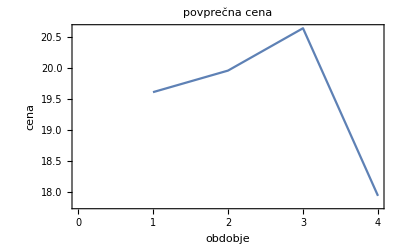

```mathematica
ListLinePlot[opvprečjaobdobja//Query[All,2],
PlotLabel->"povprečna cena", 
FrameLabel->{ "obdobje", "cena"}, 
Frame-> {{True, False}, {True, False}}
]
```

```mathematica
povprečje leta
```

```mathematica
povprečnaleto=dat12//
Query[GroupBy[#leto&]/*Values,<|
"leto"-> Query[First,"leto"],
"povprecje"->Query[Mean,"D1 (< 20 GJ)"]

|>
]
```

Dataset[<>]

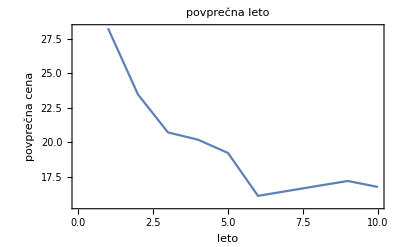

```mathematica
ListLinePlot[povprečnaleto//Query[All,2],
PlotLabel->"povprečna leto", 
FrameLabel->{ "leto", "povprečna cena"}, 
Frame-> {{True, False}, {True, False}}
]
```

povprečna leto

```mathematica
grupl=GroupBy[dat12//Query[All,All],"leto"]
```

Dataset[<>]

```mathematica
grupl1=grupl["2012"]
```

Dataset[<>]

```mathematica
leto2012=grupl1//Query[All,{2,3}]
```

Dataset[<>]

```mathematica
poglejpoletih[x_]:=grupl[x]//Query[All,3]//******
ListLinePlot[
#, 
PlotLabel->"graf za leto x", 
FrameLabel->{ "Leto", "Število vpisanih"}, 
Frame-> {{True, False}, {True, False}}
]&
```

obdobja čez leto,,,obdobja čez leta,,, povprečna cena leta,,,povprečnacena obdobja

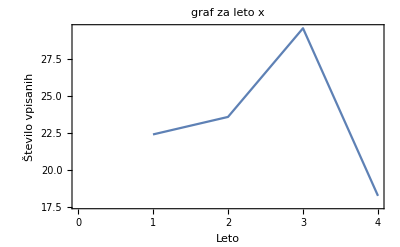

```mathematica
poglejpoletih["2013"]
```

```mathematica
1=D1
2=D2
3=D3
4=Slovenija
```

```mathematica
funkcijaextra[D_,leto_]:=data //Query[3;;, {1,1+D}] //Query[All, <| "leto" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",4], "obdobje" -> StringTake[#"STANDARDNA PORABNIŠKA SKUPINA (LETNA PORABA)",-2],#|>&]//Query[All, {1,2,4}]//
GroupBy[#//Query[All,All],"leto"]&//
#[leto]&//
Query[All,{2,3}]//********
ListLinePlot[
#, 
PlotLabel->"graf za leto x", 
FrameLabel->{ "Leto", "Število vpisanih"}, 
Frame-> {{True, False}, {True, False}}
]&
```

```mathematica
funkcijaextra[1,"2013"]
```

-Graphics-